```mathematica
(*Зададим данную функцию и построим ее график*)f[x_,y_]=3*x^2*y+y^3-12*x-15*y+3;
Plot3D[f[x,y],{x,-5,5},{y,-5,5},PlotRange->All]
```

-Graphics3D-

```mathematica
(*Локализуем точку минимума данной функции*)
G=Plot3D[f[x,y],{x,0,2},{y,1,3},PlotRange->All]
```

-Graphics3D-

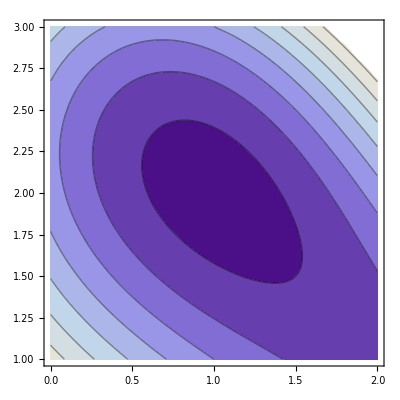

```mathematica
(*Построим линии уровня данной функции в окрестности точки минимума*)
GC=ContourPlot[f[x,y],{x,0,2},{y,1,3}]
```

```mathematica
(*Зададим точность вычислений*)
esp=10^(-5);
(*Найдем нормированный градиент данной функции*)
n[x_,y_]=Grad[f[x,y],{x,y}]/Norm[Grad[f[x,y],{x,y}]];
(*Зададим начальное приближение к точке минимума*)
M0={0,1};
(*Зададим счетчик количества итераций*)
k=0;
(*Зададим последовательность приближений к точке минимума*)
IT={Join[M0,{f[M0[[1]],M0[[2]]]}]};
(*Зададим начальную длину шага приближений точке минимума*)
lambda=1;
(*Реализуем алгоритм градиентного метода поиска экстремума*)
While[lambda≥esp,
M1=M0-lambda*N[n[M0[[1]],M0[[2]]]];
If[f[M1[[1]],M1[[2]]]<f[M0[[1]],M0[[2]]],
AppendTo[IT,Join[M1,{f[M1[[1]],M1[[2]]]}]];
M0=M1;
k=k+1,
lambda=lambda/2
];
];
(*Добавим последнюю точку в последовательность итераций*)
M1=M0-lambda*N[n[M0[[1]],M0[[2]]]];
AppendTo[IT,Join[M1,{f[M1[[1]],M1[[2]]]}]];
k=k+1;
Print["Точка минимума функции равна: ",M1]
Print["Значение функции в точке минимума равно: ",f[M1[[1]],M1[[2]]]]
Print["Количество итераций равно: ",k]
```

Точка минимума функции равна: {0.999996,2.}

Значение функции в точке минимума равно: -25.

Количество итераций равно: 11

```mathematica
(*Построим график данной функции и последовательность приближений к точке минимума в одной системе координат*)GIT3D=ListPointPlot3D[IT,PlotStyle->Red,Filling->Axis,FillingStyle->Red];
Show[G,GIT3D]
```

-Graphics3D-

```mathematica
(*Выполним анимацию последовательности приближений к точке минимума на графике данной функции*)
Animate[Show[G,ListPointPlot3D[{IT[[i]]},PlotStyle->Red,Filling->Axis,FillingStyle->Red]],{i,1,k+1,1},AnimationRunning->False]
```

```mathematica
(*Выполним анимацию полследовательности приближений к точке минимума на графике линий уровня данной функции*)Animate[Show[GC,ListPlot[{{IT[[i,1]],IT[[i,2]]}},PlotStyle->Red]],{i,1,k+1,1},AnimationRunning->False]
```